## VTI Comparison with FD

#### Compute data in x-ω space

```mathematica
<<ThinLayer`
```

```mathematica
setlayer[]:=Module[{},
tlSetLayer[1,tlCijFromThomsen[2,1,0.01,-0.05,2]];
tlSetLayer[2,tlCijFromThomsen[3,1.5,0.02,0.01,3]];
]
```

```mathematica
setlayer[]
```

```mathematica
Module[
{r=.5,layers,zs,zr,overburden,model,pcrit,dList,integrandp,toHTp,HTvec,Nfreq,deltafreq,maxfreq,ωList,toHTk},

(* ==== MODEL PARAMETERS ====*)
zs=.1;
zr=.7;
overburden=1;
layers={2};
model={overburden,Sequence@@layers};
dList={0,0};

pcrit=Flatten[N@(({#[[1]],#[[4]]}/(#[[-1]]))^(-1/2))&/@tlGetStiffness[model]];



Nfreq=200;
maxfreq=100;
deltafreq=maxfreq/Nfreq;
ωList=2Pi Range[deltafreq,maxfreq,deltafreq]//N;
freqvec=ωList;

(*===IDHT===*)
(*Module[{Noffsets=2000,pMax=4},

AbsoluteTiming[
testZ=
Table[
tlDHT2[Noffsets,toHTk[#,w]&,0,pMax w],
{w,ωList}];
]

]*)

(*===DIRECT INTEGRATION===*)
Module[{pMax,u},
pMax=Module[{pM=Max@pcrit,a=10,b=1.5},(((b-a)pM)/(ωList[[-1]]-ωList[[1]])(#-ωList[[1]])+a pM)&];

(* ==== SEISMIC RESPONSE FUNCTION ====*)
u[p_,ω_]:=tlResponseVforce[model,dList,p,ω,zs,zr,r];

DistributeDefinitions[u,pcrit,pMax,setlayer];
DistributeDefinitions["ThinLayer`"];

freqvec=ωList;
AbsoluteTiming[
test=
Transpose@ParallelTable[
setlayer[];
Quiet@NIntegrate[u[p,ω],{p,0,pMax[ω]},Method->{"GlobalAdaptive","SingularityHandler"->"DoubleExponential"},Exclusions->pcrit,MaxRecursion->15,AccuracyGoal->15,WorkingPrecision->15],
{ω,ωList}];
]
]
]
```

$Aborted

```mathematica
(*Export[NotebookDirectory[]<>"trace500mVTI.mc",Compress[{test,freqvec}],"String"];*)
(*{test,freqvec}=Uncompress@Import[NotebookDirectory[]<>"trace500mVTI.mc","String"];*)
```

#### Convert the data to x-t space

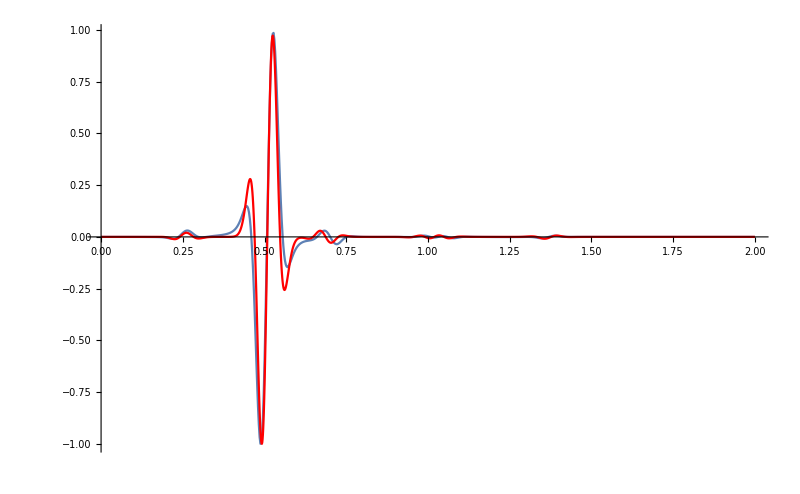

```mathematica
rickerSpectrum[w_,wp_]:=(2 w^2)/(Sqrt[π] wp^3) Exp[-(w^2/wp^2)];

Module[{u=test,ω=freqvec,FDu,i=1,int,dispfield,reflSource,fRicker=10,reflTX,t,importFD,FDdispfield,FDω,FDreflSource,FDt,FDreflTX,importFDVTI},
(*
r:1; z:2
*)

importFDVTI=BinaryReadList[NotebookDirectory[]<>"FD_VTI","Real32"];
FDu=RotateLeft[{importFDVTI[[2002;;4002]],importFDVTI[[1;;2001]]},{0,141}];
dispfield=u[[i]];
FDdispfield=FDu[[i]];

t=With[{len=Length@ω,df=(ω[[2]]-ω[[1]])/(2Pi)},Range[0,2len]/(df (2len))];FDt=With[{dt=0.001,Nt=2001},Range[0,dt (Nt-1),dt]];

reflSource=I ω dispfield(rickerSpectrum[#,2Pi fRicker]&/@ω);
reflTX=InverseFourier[{0.}~Join~reflSource~Join~Conjugate@Reverse@reflSource];
reflSource=reflSource/Max[Abs@reflSource];

Print[Show[ListLinePlot[{t,(Re@reflTX)/Max[Abs@reflTX]}ᵀ,PlotRange->{{0,2},Full},ImageSize->800],ListLinePlot[{FDt,(Re@FDdispfield)/Max[Abs@FDdispfield]}ᵀ,PlotRange->Full,PlotStyle->Red]]];

]
```

## ISO Comparison with FD

#### Compute data in x-ω space

```mathematica
<<ThinLayer`
```

```mathematica
setlayer[]:=Module[{},
tlSetLayer[1,tlCijFromThomsen[2.0002,1.0002,0,0,2.0002]];
tlSetLayer[2,tlCijFromThomsen[3.0002,1.5002,0,0,3.0002]];
]
```

```mathematica
setlayer[]
```

```mathematica
Module[
{layers,zs,zr,overburden,model,pcrit,dList,integrandp,toHTp,HTvec,Nfreq,deltafreq,maxfreq,ωList,toHTk},

(* ==== MODEL PARAMETERS ====*)
zs=.3;
zr=.4;
overburden=1;
layers={2};
model={overburden,Sequence@@layers};
dList={0,0};

pcrit=Flatten[N@(({#[[1]],#[[4]]}/(#[[-1]]))^(-1/2))&/@tlGetStiffness[model]];



Nfreq=100;
maxfreq=50;
deltafreq=maxfreq/Nfreq;
ωList=2Pi Range[deltafreq,maxfreq,deltafreq]//N;
freqvec=ωList;

(*===IDHT===*)
(*Module[{Noffsets=2000,pMax=4},

AbsoluteTiming[
testZ=
Table[
tlDHT2[Noffsets,toHTk[#,w]&,0,pMax w],
{w,ωList}];
]

]*)

(*===DIRECT INTEGRATION===*)
Module[{r=.3,pMax=1.5,u},

u[p_,ω_]:=tlResponseVforce[model,dList,p,ω,zs,zr,r];

DistributeDefinitions[u,pcrit,pMax,r,setlayer];
DistributeDefinitions["ThinLayer`"];

freqvec=ωList;
AbsoluteTiming[
test=
Transpose@ParallelTable[
setlayer[];
Quiet@NIntegrate[u[p,ω],{p,0,.9999Max@pcrit},Method->{"GlobalAdaptive","SingularityHandler"->"DoubleExponential"} ,Exclusions->pcrit,MaxRecursion->20,AccuracyGoal->15,WorkingPrecision->15],
{ω,ωList}];
]
]
]
```

{82.9523,Null}

#### Convert the data to x-t space

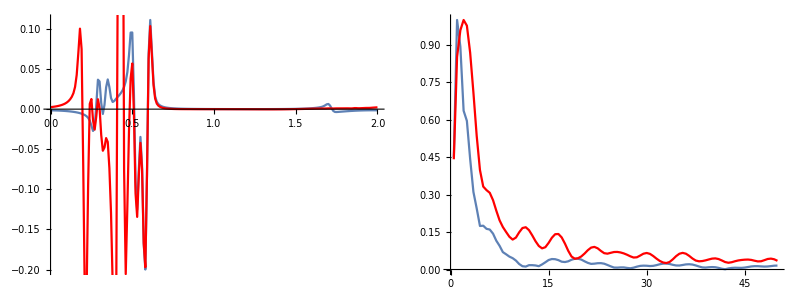

```mathematica
rickerSpectrum[w_,wp_]:=(2 w^2)/(Sqrt[π] wp^3) Exp[-(w^2/wp^2)];

Module[{u=test,ω=freqvec,FDu,i=2,int,dispfield,reflSource,fRicker=15,reflTX,t,importFD,FDdispfield,FDω,FDreflSource,FDt,FDreflTX},
(*
r:1; z:2
*)

importFD=Import[NotebookDirectory[]<>"../../ivan.txt","Data"];
{FDω,FDu}=Transpose[{#[[1]],{#[[4]]+I#[[5]],#[[2]]+I#[[3]]}}&/@importFD];

dispfield=u[[i]];
FDdispfield=Transpose[FDu][[i]];

t=With[{len=Length@ω,df=(ω[[2]]-ω[[1]])/(2Pi)},Range[0,2len]/(df (2len))];
FDt=With[{len=Length@FDω,df=(FDω[[2]]-FDω[[1]])/(2Pi)},Range[0,2len]/(df (2len))];


reflSource=dispfield(rickerSpectrum[#,2Pi fRicker]&/@ω);
FDreflSource=FDdispfield(rickerSpectrum[#,2Pi fRicker]&/@FDω);


reflTX=InverseFourier[RotateLeft[(Reverse@Conjugate@reflSource)~Join~{0+0. I}~Join~reflSource,Length@ω]];
FDreflTX=InverseFourier[RotateLeft[(Reverse@Conjugate@FDreflSource)~Join~{0+0. I}~Join~FDreflSource,Length@FDω]];

reflSource=reflSource/Max[Abs@reflSource];
FDreflSource=FDreflSource/Max[Abs@FDreflSource];



{{Show[ListLinePlot[{t,-.2(Re@reflTX)/Max[Abs@reflTX]}ᵀ,PlotRange->Full,ImageSize->Large],ListLinePlot[{FDt,(Re@FDreflTX)/Max[Abs@FDreflTX]}ᵀ,PlotRange->Full,PlotStyle->Red]],Show[ListLinePlot[{ω/(2Pi),(Abs@dispfield)/(Max@Abs@dispfield)}ᵀ,PlotRange->Full,ImageSize->Large],ListLinePlot[{FDω/(2Pi),(Abs@FDdispfield)/(Max@Abs@FDdispfield)}ᵀ,PlotRange->Full,PlotStyle->Red]]}}//TableForm


]
```

## Response of fractures

### Model parameters test

```mathematica
<<ThinLayer`
```

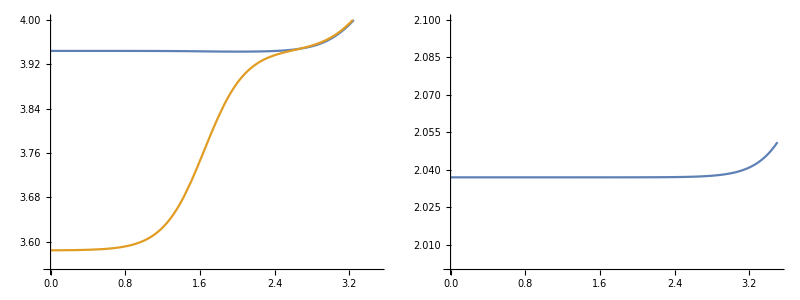

```mathematica
With[{λ=17.5 ,μ=17.5 ,ρ=2.3,ϕ=.1,kf=1.45 ,ϵ=0.1,ϵf=0.05,α=10^-5,τ=2 10^-5,lenrat=200},
cij[f_]=tlVTISquirtModuli[ϵ,ϵf,α,τ,2Pi f,lenrat][λ,μ,ρ,ϕ,kf];
Print[{{Plot[Evaluate@Abs[{√((#[[1]])/(#[[5]])),√((#[[3]])/(#[[5]]))}&@cij[10^f]],{f,0,3.5},PlotRange->{Full,{3.55,4}},ImageSize->Large],Plot[Evaluate@Abs[√((#[[4]])/(#[[5]]))&@cij[10^f]],{f,0,3.5},PlotRange->{Full,{2,2.1}},ImageSize->Large]}}//TableForm];
]
```

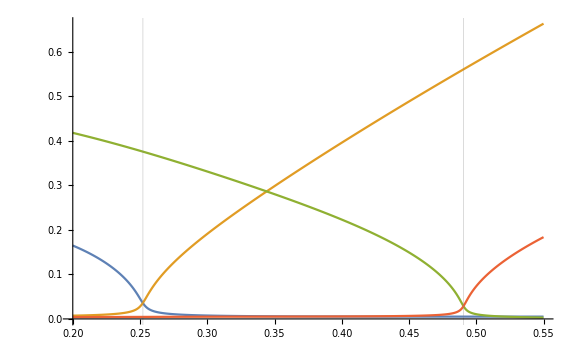

```mathematica
With[{f=10},tlSetLayer[1,cij[1000]];
Plot[Evaluate@ReIm@tlQLmatrices[1,p][[1]],{p,0.2,.55},PlotPoints->500,GridLines->{Abs[({#[[1]],#[[4]]}/(#[[-1]]))^(-1/2)&@tlGetStiffness[1]],None},ImageSize->Large]]
```

#### Compute data in x-ω space

```mathematica
<<ThinLayer`
```

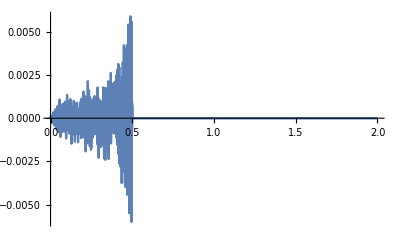

```mathematica
computeResponse[Nrep_,Nfreq_,maxfreq_,lenrat_]:=
Module[{r=.5,zs=.4,zb=.8,D2=.6,layers,overburden,model,dList,integrandp,toHTp,HTvec,deltafreq,ωList,toHTk,setlayer,pMax,u,pcrit,UzUr,time},
(* ==== MODEL PARAMETERS ====*)
overburden=1;
layers={2}~Join~(Sequence@@@ConstantArray[{3,2},Nrep])~Join~{3};
dList={0}~Join~ConstantArray[D2/(Length@layers-1),Length@layers-1]~Join~{0};
model={overburden,Sequence@@layers};

setlayer[ω_]:=Module[
{λ=17.5 ,μ=17.5 ,ρ2=2.3,ϕ=.1,kf=1.45 ,ϵ=0.1,ϵf=0.05,α=10^-5,τ=2 10^-5,cij,vp1=2.5,vs1=2.0,ρ1=2.},
cij=tlVTISquirtModuli[ϵ,ϵf,α,τ,ω,lenrat][λ,μ,ρ2,ϕ,kf];
tlSetLayer[1,tlCijFromThomsen[vp1,vs1,0,0,ρ1]];
tlSetLayer[2,cij];
tlSetLayer[3,{λ+2μ,λ,λ+2μ,μ,ρ2}];
];

pcrit:=Flatten[N@(({#[[1]],#[[4]]}/(#[[-1]]))^(-1/2))&/@tlGetStiffness[DeleteDuplicates@model]];
pMax[ω_,pM_]:=Module[{a=25,b=2},
(((b-a)pM)/(ωList[[-1]]-ωList[[1]])(ω-ωList[[1]])+a pM)];


deltafreq=maxfreq/Nfreq;
ωList=2Pi Range[deltafreq,maxfreq,deltafreq]//N;

(*===DIRECT INTEGRATION===*)


u[p_,ω_]:=tlResponseVforce[model,dList,p,ω,zs,zb,r];

DistributeDefinitions[u,setlayer,pMax,pcrit];
DistributeDefinitions["ThinLayer`"];

time=AbsoluteTiming[
UzUr=
Transpose@ParallelTable[
(* ==== MODEL ASSIGNMENT ==== *)
setlayer[ω];
(* ==== INTEGRATION ==== *)
Quiet@NIntegrate[u[p,ω],{p,0,pMax[ω,Max@Abs@pcrit]},Method->{"GlobalAdaptive","SingularityHandler"->"DoubleExponential"},Exclusions->pcrit,MaxRecursion->15,AccuracyGoal->15,WorkingPrecision->15],
{ω,ωList}];
][[1]];

Print["It took me "<>ToString[Round[time/60]]<>" minutes"];
{ωList,UzUr}

(*===IDHT===*)
(*Module[{Noffsets=2000,pMax=4},
AbsoluteTiming[
testZ=
Table[
tlDHT2[Noffsets,toHTk[#,w]&,0,pMax w],
{w,ωList}];]]*)
]
computeResponse[0,300,150,200]
```

```mathematica
{freqvec,test1}=computeResponse[0,300,150,200];
```

It took me 239 minutes

```mathematica
(*Export[NotebookDirectory[]<>"traceL200_Nrep0.mc",Compress[{test1,freqvec}],"String"];*)
```

```mathematica
{freqvec,test2}=computeResponse[0,300,150,100];
```

It took me 240 minutes

```mathematica
(*Export[NotebookDirectory[]<>"traceL100_Nrep0.mc",Compress[{test2,freqvec}],"String"];*)
```

```mathematica
(*{test2,freqvec}=Uncompress@Import[NotebookDirectory[]<>"traceL100_Nrep0.mc"];*)
```

#### Convert the data to x-t space

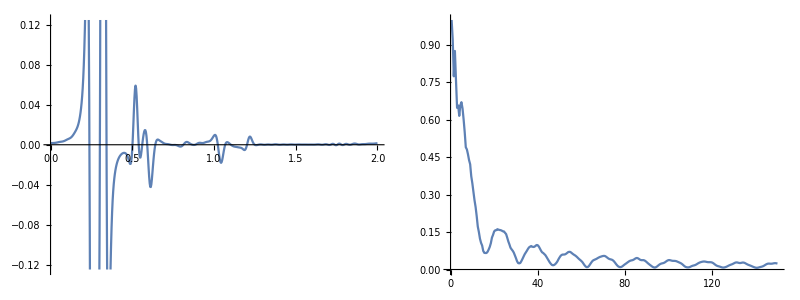

```mathematica
rickerSpectrum[w_,wp_]:=(2 w^2)/(Sqrt[π] wp^3) Exp[-(w^2/wp^2)];

Module[{u=test2,ω=freqvec,FDu,i=2,int,dispfield,reflSource,fRicker=15,reflTX,t,importFD,FDdispfield,FDω,FDreflSource,FDt,FDreflTX},
(*
r:1; z:2
*)

dispfield=u[[i]];

t=With[{len=Length@ω,df=(ω[[2]]-ω[[1]])/(2Pi)},Range[0,2len]/(df (2len))];


reflSource=dispfield(rickerSpectrum[#,2Pi fRicker]&/@ω);


reflTX=InverseFourier[{0.}~Join~reflSource~Join~Conjugate@Reverse@reflSource];


{{ListLinePlot[{t,(Re@reflTX)/Max[Abs@reflTX]}ᵀ,PlotRange->{{0,2},{-1,1}.125},ImageSize->Large],ListLinePlot[{ω/(2Pi),(Abs@dispfield)/(Max@Abs@dispfield)}ᵀ,PlotRange->Full,ImageSize->Large]}}//TableForm


]
```

## Other tests

InterpolatingFunction::dmval: Input value {0.3} lies outside the range of data in the interpolating function. Extrapolation will be used.

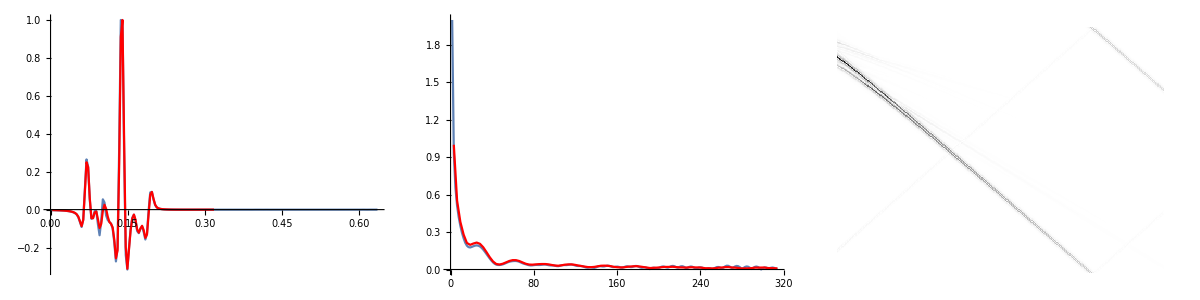

```mathematica
rickerSpectrum[w_,wp_]:=(2 w^2)/(Sqrt[π] wp^3) Exp[-(w^2/wp^2)];

Module[{u=testZ,Noff=300,maxX,minX,int,regoffsets,regRefl,reflSource,fRicker=15,reflTX,t,ivant,trace300W,trace300T,trace300WSource},
{maxX,minX}={Min@Re@u[[;;,-1,1]],Max@Re@u[[;;,1,1]]};

int=Table[Interpolation[u[[i,;;,;;]],InterpolationOrder->3,Method->"Hermite"],{i,1,Dimensions[u][[1]]}];
regoffsets=Range[minX,maxX,(maxX-minX)/Noff]//N;
regRefl=Table[int[[i]][#]&/@regoffsets,{i,1,Dimensions[u][[1]]}];
(*regRefl=u[[;;,;;,2]];*)

reflSource=regRefl(rickerSpectrum[#,2Pi fRicker]&/@freqvec);

reflTX=Table[
InverseFourier[RotateLeft[(Reverse@Conjugate@reflSource[[;;,i]])~Join~{0+0. I}~Join~reflSource[[;;,i]],Length@freqvec]]
,{i,1,Dimensions[reflSource][[2]]}];

t=Range[2Length[freqvec]+1]/((freqvec[[2]]-freqvec[[1]]) Length[freqvec]);

testTX=reflTX;
testWX=regRefl;
offsets=regoffsets;
dpdata={Flatten@ConstantArray[offsets,Length@t],Flatten@ConstantArray[t,Length@offsets],Flatten@testTX}ᵀ;


(*=== COMAPRISON WITH IVAN'S SOLUTION ===*)

importIvan=Quiet@Import[NotebookDirectory[]<>"..\..\ivan.txt","Data"];
{ivanω,ivanUz}=Transpose[{#[[1]],#[[2]]+I#[[3]]}&/@importIvan];
ivant=Range[Length[ivanω]]/((ivanω[[2]]-ivanω[[1]]) Length[ivanω]);

reflSourceIvan= ivanUz(rickerSpectrum[#,2Pi fRicker]&/@ivanω);
reflSourceIvan=reflSourceIvan/Max[Abs@reflSourceIvan];
reflTXIvan=
InverseFourier[RotateLeft[(Reverse@Conjugate@reflSourceIvan)~Join~{0+0. I}~Join~reflSourceIvan,Length@ivanω]][[1;;Length@ivanω]];

trace300W=Table[int[[i]][.3],{i,1,Dimensions[u][[1]]}];
trace300WSource=trace300W(rickerSpectrum[#,2Pi fRicker]&/@freqvec);
trace300T=InverseFourier[RotateLeft[(Reverse@Conjugate@trace300WSource)~Join~{0+0. I}~Join~trace300WSource,Length@freqvec]][[1;;Length@freqvec]];


(*{{Show[ListLinePlot[{t,(Re@trace300T)/(Max@Abs@trace300T)}ᵀ,PlotRange->Full,ImageSize->Large],ListLinePlot[{ivant,(Re@reflTXIvan)/(Max@Abs@reflTXIvan)}ᵀ,PlotRange->Full,PlotStyle->Red]],
Show[ListLinePlot[{freqvec,((Length@freqvec/Length@ivanω)Abs@trace300W)/(Max@Abs@trace300W)}ᵀ,PlotRange->Full,ImageSize->Large],ListLinePlot[{ivanω,(Abs@ivanUz)/(Max@Abs@ivanUz)}ᵀ,PlotRange->Full,PlotStyle->Red]],ArrayPlot[(reflTX[[;;,;;]])ᵀ,ImageSize->Large]}}//TableForm*)
ListDensityPlot[dpdata]
]
```

```mathematica
Manipulate[ListLinePlot[Re@testTX[[i,;;]],PlotRange->Full,PlotLabel->"X = "<>ToString[1000offsets[[i]]]<>" m"],{i,1,Dimensions[testTX][[1]],1}]
```

Part::partd: Part specification testTX⟦1,1;;All⟧ is longer than depth of object.

Part::partd: Part specification offsets⟦1⟧ is longer than depth of object.

ListLinePlot::lpn: Re[testTX⟦1,1;;All⟧] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

```mathematica
Manipulate[ListLinePlot[Abs@testWX[[;;,i]],PlotRange->Full,PlotLabel->"X = "<>ToString[1000offsets[[i]]]<>" m"],{i,1,Dimensions[testWX][[2]],1}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partd: Part specification offsets⟦1⟧ is longer than depth of object.

ListLinePlot::lpn: Abs[Symbol[]] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

```mathematica
With[{rmax=Min@Re@testZ[[;;,-1,1]],rmin=Max@Re@testZ[[;;,1,1]],r=Range[Max@Re@testZ[[;;,1,1]],Min@Re@testZ[[;;,-1,1]],(Min@Re@testZ[[;;,-1,1]]-Max@Re@testZ[[;;,1,1]])/(Dimensions[testZ][[2]]-1)]//N,int=Table[Interpolation[testZ[[i,;;,;;]],InterpolationOrder->3,Method->"Hermite"],{i,1,Dimensions[testZ][[1]]}]},
dpdata={Flatten@testZ[[;;,;;,1]],Flatten@Transpose@ConstantArray[freqvec,Dimensions[testZ][[2]]]}ᵀ;
regGrid={Flatten@ConstantArray[r,Dimensions[testZ][[1]]],Flatten@Transpose@ConstantArray[freqvec,Dimensions[testZ][[2]]]}ᵀ;



{Manipulate[
Show[ListPlot[dpdata,PlotRange->{{0,xmax},Automatic},ScalingFunctions->{Identity,"Reverse"},ImageSize->Large],
ListPlot[regGrid,PlotRange->{{0,xmax},Automatic},ScalingFunctions->{Identity,"Reverse"},PlotStyle->Red]]
,{xmax,.5rmin,1.5rmax}],

Manipulate[
Show[
ListLinePlot[{testZ[[i,;;,1]],Im@testZ[[i,;;,2]]}ᵀ,ImageSize->Large,PlotRange->{{rmin,rmax},Full}],
ListPlot[{r,Im@int[[i]][r]}ᵀ,PlotStyle->Red]
],{i,1,Dimensions[testZ][[1]],1}]}

]
```

## Notes and comments

```mathematica
(*

(*==== MULLER ====*)

U[ω_,k_]:=Reverse@DiagonalMatrix[tlQLmatrices[overburden,k/ω][[1]]]+DiagonalMatrix[{k/ω,-k/ω}];
J[k_,r_]:=DiagonalMatrix[{BesselJ[1,k r],BesselJ[0,k r]}];
Su[ω_,k_]:={-k/ω,(k/ω)^2/tlQLmatrices[overburden,k/ω][[1,2]]}Exp[ⅈ ω zs tlQLmatrices[overburden,k/ω][[1]]];
Sd[ω_,k_]:={k/ω,(k/ω)^2/tlQLmatrices[overburden,k/ω][[1,2]]}Exp[-ⅈ ω zs tlQLmatrices[overburden,k/ω][[1]]];
ref[ω_,k_]:=(DiagonalMatrix[Exp[I ω tlQLmatrices[overburden,k/ω][[1]] zr]].tlReflectivity[model,dList,k/ω,ω].DiagonalMatrix[Exp[I ω tlQLmatrices[overburden,k/ω][[1]] zr]])//Chop;
integrand[ω_,k_]:={{-1,0},{0,ⅈ}}.U[ω,k].(Su[ω,k]+ref[ω,k].Sd[ω,k]);*)

(*U[p_]:=(*Reverse@DiagonalMatrix[tlQLmatrices[overburden,p][[1]]]+*)DiagonalMatrix[{p,-p}];
J[p_,ω_,r_]:=DiagonalMatrix[{N@BesselJ[1,p ω r],N@BesselJ[0,p ω r]}];
Su[p_,ω_]:={-1,p/tlQLmatrices[overburden,p][[1,2]]}Exp[ⅈ ω zs tlQLmatrices[overburden,p][[1]]];
Sd[p_,ω_]:={1,p/tlQLmatrices[overburden,p][[1,2]]}Exp[-ⅈ ω zs tlQLmatrices[overburden,p][[1]]];
ref[p_,ω_]:=(DiagonalMatrix[Exp[I ω tlQLmatrices[overburden,p][[1]] zr]].tlReflectivity[model,dList,p,ω]ᵀ.DiagonalMatrix[Exp[I ω tlQLmatrices[overburden,p][[1]] zr]])//Chop;
(*f2[p_,ω_]:=ω({{-1,0},{0,ⅈ}}).U[p].(Su[p,ω]+ref[p,ω].Sd[p,ω])/4./Pi/ρ//Chop;*)
f2[p_,ω_,r_]:=p(J[p,ω,r]{{-1,0},{0,ⅈ}}).U[p].(Su[p,ω]+ref[p,ω].Sd[p,ω])//Chop;
*)
(*
ref[p_,ω_]=(DiagonalMatrix[Exp[I ω tlQLmatrices[overburden,p][[1]] zr]].tlReflectivity[model,dList,p,ω].DiagonalMatrix[Exp[I ω tlQLmatrices[overburden,p][[1]] zr]])//N;

(*==== URSIN ====
stress-displacement as in Stovas and Ursin:
b = [ω Uz, -Sr, Sz, ωUr] ;
Tranformed back to space-time:
b = [uz, σrz, σzz, ur] ;

*)

Σ1[p_,ω_]=1/(√2)tlQLmatrices[overburden,p][[2]]ᵀ.{-1/(ρ ω) ,0};(*σzz force*)
Σ2[p_,ω_]=Σ1[p,ω];
S1[p_,ω_]=DiagonalMatrix[Exp[I ω tlQLmatrices[overburden,p][[1]] zs]].Σ1[p,ω];
S2[p_,ω_]=DiagonalMatrix[Exp[-I ω tlQLmatrices[overburden,p][[1]] zs]].Σ2[p,ω];
U[p_,ω_]=ref[p,ω].S2[p,ω]-S1[p,ω];
B[p_,ω_]={Sequence@@((I tlQLmatrices[overburden,p][[2]])/(√2).U[p,ω]),Sequence@@((tlQLmatrices[overburden,p][[3]])/(√2).U[p,ω])};
b[p_,ω_,r_]=p ω^2 B[p,ω]{1/ω,-1,1,1/ω}{BesselJ[0,p ω r],BesselJ[1,p ω r],BesselJ[0,p ω r],BesselJ[1,p ω r]};

(*{ur,uz}*)
u[p_,ω_,r_]=b[p,ω,r][[{4,1}]];
(*{σrz,σzz}*)
σ[p_,ω_,r_]=b[p,ω,r][[{2,3}]];
*)
(*FindMaxK[ω_,tol_]:=Module[{kmax,phase},
kmax=phorlayer1 ω;
phase[k_]:=(DiagonalMatrix[E^(I ω tlQLmatrices[overburden,k/ω][[1]] zr)].DiagonalMatrix[E^(I ω tlQLmatrices[overburden,k/ω][[1]] zs)])[[1,1]];
FindMinimum[{Abs[phase[k]],k>0},{k,kmax},AccuracyGoal->tol][[2,1,2]]
];*)


(*With[{p0=.1,ω=2Pi 20,r=.3},
tlResponse[model,dList,p0,ω,zs,zr]
]*)

(*Module[

{Np=5000,pmax=4,pList,dp,r=.3},
dp=pmax/Np;
pList=Range[0,pmax,dp];

DistributeDefinitions[pList,ωList,dp,integrand];

freqvec=ωList;
AbsoluteTiming[
testZ=
ParallelTable[
dp Total[integrand[#,ω,r][[1]]&/@pList],
{ω,ωList},DistributedContexts->{"ThinLayer`Private`"}];
]
]*)


(*AbsoluteTiming[
testZ=
Table[
tlDHT2[Noffsets,ref[#,ωList[[i]]][[1,1]]&,0,pMax],
{i,1,Length@ωList}];


freqvec=ωList;
]*)


(*Table[
Module[{ω0=ωList[[i]],testk},
{testk=FindMaxK[ω0,11],ListLinePlot[Transpose[ReIm@ref[ω0,#]&/@Range[.5testk,1.5testk,testk/100]],ImageSize->600,PlotRange->Full]}
]
,{i,Length@ωList}]
*)


(*With[{ω=2Pi 300, tol=10},
K=FindMaxK[ω,tol];
{ref[ω,#]&/@Range[0,K,K/(Noffsets-1)],K}
]*)


(*With[{ω=2.Pi 150},
{ListLinePlot[(ReIm@tlDHT2[Noffsets,ref[ω,#]&,0,kMax][[;;,2]])ᵀ,PlotLabel->kMax,ImageSize->Large,PlotRange->Full],
ListLinePlot[(ReIm@tlDHT2[Noffsets,ref[ω,#]&,0,FindMaxK[ω,11]][[;;,2]])ᵀ,PlotLabel->FindMaxK[ω,11],ImageSize->Large,PlotRange->Full]}
]*)
```